## Problem 1

```mathematica
f=Log[1/2^n]+n*Log[n]-n-((x*Log[x]-x)+((n-x)*Log[n-x])-(n-x))
```

Log[2^-n]+n Log[n]-(n-x) Log[n-x]-x Log[x]

```mathematica
p[x_]:=Log[1/2^n]+n*Log[n]-n-((x*Log[x]-x)+((n-x)*Log[n-x])-(n-x))
```

```mathematica
D[f,x]
```

Log[n-x]-Log[x]

```mathematica
p[n/2+delta/2]-1/2*p[n/2]
```

Log[2^-n]-(-delta/2+n/2) Log[-delta/2+n/2]-(delta/2+n/2) Log[delta/2+n/2]+n Log[n]+1/2 (-Log[2^-n]+n Log[n/2]-n Log[n])

```mathematica
Simplify[Log[2^-n]-(-delta/2*(Log[n/2]-delta/n))-(n/2*((Log[n/2]-delta/n)))-(delta/2*(Log[n/2+delta/n]))-(n/2*(Log[n/2+delta/n]))+n Log[n]+1/2 (-Log[2^-n]+n Log[n/2]-n Log[n])]
```

1/(2 n)(-delta^2+delta n+n Log[2^-n]-n (delta+n) Log[delta/n+n/2]+delta n Log[n/2]+n^2 Log[n])

```mathematica
Simplify[1/(2 n)*(-delta^2+delta n+n Log[2^-n]-n (delta+n)*(Log[n/2]+delta/2)+delta n Log[n/2]+n^2 Log[n])]
```

(-delta (-2+n) n-delta^2 (2+n)+n^2 Log[4]+2 n Log[2^-n])/(4 n)

```mathematica
Solve[%==0,delta]
```

{{delta→(2 n-n^2-√((2-n)^2 n^2-4 (-2-n) (n^2 Log[4]+2 n Log[2^-n])))/(2 (2+n))},{delta→(2 n-n^2+√((2-n)^2 n^2-4 (-2-n) (n^2 Log[4]+2 n Log[2^-n])))/(2 (2+n))}}

## Problem 2

### Part A

```mathematica
headsup[flips_Integer]:=
Module[{p,n=flips,x,plist},
plist={};
For[x=0,x<n+1,x++,AppendTo[plist,1/2^n*(n!)/(x!*(n-x)!)]];
plist
]
```

```mathematica
headsup[2]
```

{1/4,1/2,1/4}

### Part B

```mathematica
headsup[flips_Integer]:=
Module[{pmax,n=flips,x,plistx,plisty,p,finallist},
pmax=1/2;
plistx={};
plisty={};
For[x=0,x<n+1,x++,AppendTo[plistx,x/flips]];
For[x=0,x<n+1,x++,AppendTo[plisty,((1/2^n*(n!)/(x!*(n-x)!))/(1/2^n*(n!)/((n/2)!*(n-n/2)!)))]];
finallist={plistx,plisty};
Transpose[finallist]
]
```

```mathematica
headsup[2]
```

{{0,1/2},{1/2,1},{1,1/2}}

```mathematica
headsup[20]
```

{{0,1/184756},{1/20,5/46189},{1/10,5/4862},{3/20,15/2431},{1/5,15/572},{1/4,12/143},{3/10,30/143},{7/20,60/143},{2/5,15/22},{9/20,10/11},{1/2,1},{11/20,10/11},{3/5,15/22},{13/20,60/143},{7/10,30/143},{3/4,12/143},{4/5,15/572},{17/20,15/2431},{9/10,5/4862},{19/20,5/46189},{1,1/184756}}

### Part C

```mathematica
list20=headsup[20];
list100=headsup[100];
list1000=headsup[1000];
```

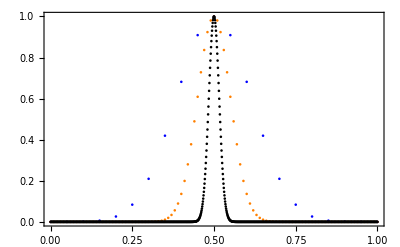

```mathematica
ListPlot[{list20,list100,list1000},Frame->True,PlotRange->All,PlotStyle->{{Blue},{Dashed,Orange},{Dotted,Black}}]
```